```mathematica
RandomPSD[n_]:=Module[{X},X=RandomComplex[{-1-ⅈ,+1+ⅈ},{n,n}];ConjugateTranspose[X].X]
```

```mathematica
RandomPSD[3]
```

{{1.15615+0. ⅈ,0.0221559+1.02335 ⅈ,0.800478+0.372444 ⅈ},{0.0221559-1.02335 ⅈ,1.45862+0. ⅈ,0.767043-0.988943 ⅈ},{0.800478-0.372444 ⅈ,0.767043+0.988943 ⅈ,1.15666+0. ⅈ}}

```mathematica
RandomTetra[n_]:=Module[{A,B,D},
A=RandomPSD[n];
B=RandomPSD[n];
D=RandomPSD[n];
{A,B,A+B,D,A+B+D,B+D}
]
```

```mathematica
Map[Eigenvalues,RandomTetra[4]]
```

{{6.47666,2.31371,0.90367,0.0992786},{4.11703,3.09208,1.6207,0.270172},{8.2499,5.86689,3.15655,1.61997},{6.68641,2.97873,1.56986,0.0346164},{12.6565,8.96575,5.82205,2.71861},{10.2607,5.83586,2.73495,1.53812}}

```mathematica
Map[SymmetricPolynomial[2,Eigenvalues[#]]&,RandomTetra[4]]
```

{18.3202,56.403,151.48,38.8774,377.498,211.406}

```mathematica
SraESPIneq[k_,sextuple_]:=Module[{f},f=SymmetricPolynomial[k,Eigenvalues[sextuple⟦#⟧]]&;
f[3]*f[6]-f[2]*f[5]
]
```

```mathematica
SraESPIneqConjecture[k_,sextuple_]:=
Module[{f},
f=SymmetricPolynomial[k,Eigenvalues[sextuple⟦#⟧]]&;
(f[3]*f[6])^(1/k)-(f[2]*f[5])^(1/k)-(f[1]*f[4])^(1/k)
]
```

```mathematica
SraESPIneqConjecture[4,RandomTetra[4]]
```

6.07802

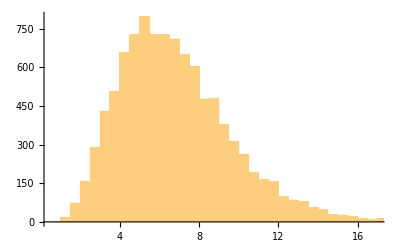

```mathematica
Histogram[Map[SraESPIneqConjecture[4,RandomTetra[4]]&,Range[10000]]]
```

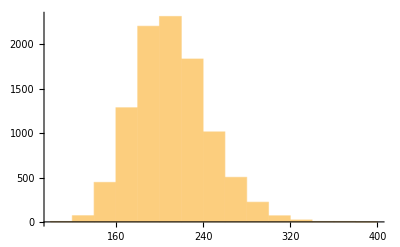

```mathematica
Histogram[Map[SraESPIneqConjecture[2,RandomTetra[10]]&,Range[10000]]]
```

```mathematica
Expand[SymmetricPolynomial[1,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]^2-SymmetricPolynomial[1,{Subscript[x, 1]^2,Subscript[x, 2]^2,Subscript[x, 3]^2}]]
```

2 x_1 x_2+2 x_1 x_3+2 x_2 x_3

```mathematica
WackyIdentityChecking[k_,sextuple_]:=
Module[{f},
f=SymmetricPolynomial[k,Eigenvalues[sextuple⟦#⟧]]&;
(f[3]*f[6])-(f[2]*f[5])-(f[1]*f[4])
]
```

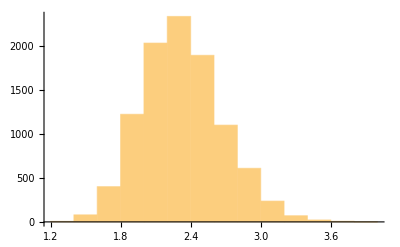

```mathematica
Histogram[Map[WackyIdentityChecking[2,RandomTetra[10]]&,Range[10000]]]
```